## V to I Transfer Function

### Transfer function

#### Old:

```mathematica
Solve[(1/Rg+(1-g)/Rf) Zt==g-((g-1)/Rf+g/Rs) s L,{g}]
```

```mathematica
{{g->-(Rs (L Rg s-Rf Zt-Rg Zt))/(Rg (Rf Rs-L Rf s-L Rs s+Rs Zt))}}
```

{{g→-(Rs (L Rg s-Rf Zt-Rg Zt))/(Rg (Rf Rs-L Rf s-L Rs s+Rs Zt))}}

```mathematica
Zt[s_]:=Rt/(1+ⅈ s Rt Ct)
```

```mathematica
FullSimplify[(Zt[s]+(ⅈ L s/(g1)))/(Zt[s]+ⅈ L s g2+Rf)*(Conjugate[Zt[s]]-(ⅈ L s/(g1)))/(Conjugate[Zt[s]]-ⅈ L s g2+Rf),Assumptions->{s∈Reals,Rt∈Reals,Ct∈Reals}]
```

(L^2 s^2+Rt^2 (g1-Ct L s^2)^2)/(g1^2 (2 Rf Rt+g2^2 L^2 s^2+Rt^2 (-1+Ct g2 L s^2)^2+Rf^2 (1+Ct^2 Rt^2 s^2)))

```mathematica
G[s_,L_]:=Sqrt[(L^2 s^2+850000^2 (10-10^-12 L s^2)^2)/(2 866 850000+88^2 L^2 s^2+850000^2 (-1+10^-12 88 L s^2)^2+866^2 (1+(10^-12)^2 850000^2 s^2))]
```

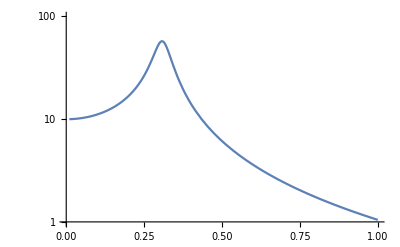

```mathematica
LogPlot[G[2 π f,300 10^-9],{f,10^6,10^8}, PlotRange->{1,100}]
```

#### Using Kirchoff, Rm = 0

```mathematica
(* Use Kirchoff's rules to get transfer function *)
Eliminate[Vo-Vs==Io s Lc&& Vs==Is Rs&&Vs-Vin==Iff Rf&&Io==Iff+Is&&Vo/(Rt/(1+s Rt Ct))+Iff==Ig&&Vin==Ig (Rg+s Lg),{Io,Is,Ig,Iff,Vo}]
(* With complex numbers *)
Eliminate[Vo-Vs==Io ⅈ s Lc&& Vs==Is Rs&&Vs-Vin==Iff Rf&&Io==Iff+Is&&Vo/(Rt/(1+ⅈ s Rt Ct))+Iff==Ig&&Vin==Ig (Rg+ⅈ s Lg),{Io,Is,Ig,Iff,Vo}]
```

Rs (Rf+Rg+Lg s+(Lc Rg s)/Rt+Ct Lc Rg s^2+(Lc Lg s^2)/Rt+Ct Lc Lg s^3) Vin==(Rg Rs+(Rf Rg Rs)/Rt+Lg Rs s+Ct Rf Rg Rs s+(Lc Rf Rg s)/Rt+(Lg Rf Rs s)/Rt+(Lc Rg Rs s)/Rt+Ct Lc Rf Rg s^2+Ct Lg Rf Rs s^2+Ct Lc Rg Rs s^2+(Lc Lg Rf s^2)/Rt+(Lc Lg Rs s^2)/Rt+Ct Lc Lg Rf s^3+Ct Lc Lg Rs s^3) Vs&&Rt≠0

Rs (-Rf-Rg-ⅈ Lg s-(ⅈ Lc Rg s)/Rt+Ct Lc Rg s^2+(Lc Lg s^2)/Rt+ⅈ Ct Lc Lg s^3) Vin==(-Rg Rs-(Rf Rg Rs)/Rt-ⅈ Lg Rs s-ⅈ Ct Rf Rg Rs s-(ⅈ Lc Rf Rg s)/Rt-(ⅈ Lg Rf Rs s)/Rt-(ⅈ Lc Rg Rs s)/Rt+Ct Lc Rf Rg s^2+Ct Lg Rf Rs s^2+Ct Lc Rg Rs s^2+(Lc Lg Rf s^2)/Rt+(Lc Lg Rs s^2)/Rt+ⅈ Ct Lc Lg Rf s^3+ⅈ Ct Lc Lg Rs s^3) Vs&&Rt≠0

```mathematica
Factor[Rs (Rf+Rg+Lg s+(Lc Rg s)/Rt+Ct Lc Rg s^2+(Lc Lg s^2)/Rt+Ct Lc Lg s^3)/(Rg Rs+(Rf Rg Rs)/Rt+Lg Rs s+Ct Rf Rg Rs s+(Lc Rf Rg s)/Rt+(Lg Rf Rs s)/Rt+(Lc Rg Rs s)/Rt+Ct Lc Rf Rg s^2+Ct Lg Rf Rs s^2+Ct Lc Rg Rs s^2+(Lc Lg Rf s^2)/Rt+(Lc Lg Rs s^2)/Rt+Ct Lc Lg Rf s^3+Ct Lc Lg Rs s^3)]
Factor[Rs (-Rf-Rg-ⅈ Lg s-(ⅈ Lc Rg s)/Rt+Ct Lc Rg s^2+(Lc Lg s^2)/Rt+ⅈ Ct Lc Lg s^3)/(-Rg Rs-(Rf Rg Rs)/Rt-ⅈ Lg Rs s-ⅈ Ct Rf Rg Rs s-(ⅈ Lc Rf Rg s)/Rt-(ⅈ Lg Rf Rs s)/Rt-(ⅈ Lc Rg Rs s)/Rt+Ct Lc Rf Rg s^2+Ct Lg Rf Rs s^2+Ct Lc Rg Rs s^2+(Lc Lg Rf s^2)/Rt+(Lc Lg Rs s^2)/Rt+ⅈ Ct Lc Lg Rf s^3+ⅈ Ct Lc Lg Rs s^3)]
```

(Rs (Rf Rt+Rg Rt+Lc Rg s+Lg Rt s+Lc Lg s^2+Ct Lc Rg Rt s^2+Ct Lc Lg Rt s^3))/((Rg+Lg s) (Rf Rs+Rs Rt+Lc Rf s+Lc Rs s+Ct Rf Rs Rt s+Ct Lc Rf Rt s^2+Ct Lc Rs Rt s^2))

(Rs (Rf Rt+Rg Rt+ⅈ Lc Rg s+ⅈ Lg Rt s-Lc Lg s^2-Ct Lc Rg Rt s^2-ⅈ Ct Lc Lg Rt s^3))/((Rg+ⅈ Lg s) (Rf Rs+Rs Rt+ⅈ Lc Rf s+ⅈ Lc Rs s+ⅈ Ct Rf Rs Rt s-Ct Lc Rf Rt s^2-Ct Lc Rs Rt s^2))

```mathematica
(* Transfer function without Lg *)
FullSimplify[(Rs (Rf Rt+Rg Rt+Lc Rg s+Lg Rt s+Lc Lg s^2+Ct Lc Rg Rt s^2+Ct Lc Lg Rt s^3))/((Rg+Lg s) (Rf Rs+Rs Rt+Lc Rf s+Lc Rs s+Ct Rf Rs Rt s+Ct Lc Rf Rt s^2+Ct Lc Rs Rt s^2))/.Lg->0]
FullSimplify[(Rs (Rf Rt+Rg Rt+ⅈ Lc Rg s+ⅈ Lg Rt s-Lc Lg s^2-Ct Lc Rg Rt s^2-ⅈ Ct Lc Lg Rt s^3))/((Rg+ⅈ Lg s) (Rf Rs+Rs Rt+ⅈ Lc Rf s+ⅈ Lc Rs s+ⅈ Ct Rf Rs Rt s-Ct Lc Rf Rt s^2-Ct Lc Rs Rt s^2))/.Lg->0]
```

(Rs (Rf Rt+Rg (Rt+Lc s+Ct Lc Rt s^2)))/(Rg (Rf (Rs+Lc s) (1+Ct Rt s)+Rs (Rt+Lc s+Ct Lc Rt s^2)))

(Rs (-(Rf+Rg) Rt-ⅈ Lc Rg s+Ct Lc Rg Rt s^2))/(Rg (-Rs (Rf+Rt)-ⅈ (Lc (Rf+Rs)+Ct Rf Rs Rt) s+Ct Lc (Rf+Rs) Rt s^2))

```mathematica
(* Verify gain at DC is correct *)
Simplify[(Rs (Rf Rt+Rg (Rt+Lc s+Ct Lc Rt s^2)))/(Rg (Rf (Rs+Lc s) (1+Ct Rt s)+Rs (Rt+Lc s+Ct Lc Rt s^2)))/.s->0]
Simplify[(-(Rf+Rg)-ⅈ Lc Rg s/Rt+Ct Lc Rg s^2)/(Rg (-(Rf/Rt+1)-ⅈ (Lc (Rf/Rs+1)/Rt+Ct Rf) s+Ct Lc (Rf/Rs+1) s^2))/.s->0]
```

((Rf+Rg) Rt)/(Rg (Rf+Rt))

((Rf+Rg) Rt)/(Rg (Rf+Rt))

```mathematica
(* Verify that taking Lc/Rt -> 0 and Lc Ct -> 0 is valid *)
FullSimplify[Sqrt[(-(Rf+Rg)-ⅈ Lc Rg s/Rt+Ct Lc Rg s^2)/(Rg (-(Rf/Rt+1)-ⅈ (Lc (Rf/Rs+1)/Rt+Ct Rf) s+Ct Lc (Rf/Rs+1) s^2)) (-(Rf+Rg)+ⅈ Lc Rg s/Rt+Ct Lc Rg s^2)/(Rg (-(Rf/Rt+1)+ⅈ (Lc (Rf/Rs+1)/Rt+Ct Rf) s+Ct Lc (Rf/Rs+1) s^2))],Assumptions->{s∈Reals,Rt∈Reals,Ct∈Reals,Rg∈Reals,Rf∈Reals,Rs∈Reals,Lc∈Reals}]
```

√((Rs^2 (Rf Rt+Rg (Rt-ⅈ Lc s-Ct Lc Rt s^2)) (Rf Rt+Rg (Rt+ⅈ Lc s-Ct Lc Rt s^2)))/(Rg^2 (Rs^2 (Rf+Rt)^2+(Lc^2 (Rf+Rs)^2+Ct Rs (Ct Rf^2 Rs-2 Lc (Rf+Rs)) Rt^2) s^2+Ct^2 Lc^2 (Rf+Rs)^2 Rt^2 s^4)))

```mathematica
(* Program and plot *)
G0[Rf_,Rg_,Rs_,Rt_,Lc_,Ct_,s_]:=√((Rs^2 (Rf Rt+Rg (Rt-ⅈ Lc s-Ct Lc Rt s^2)) (Rf Rt+Rg (Rt+ⅈ Lc s-Ct Lc Rt s^2)))/(Rg^2 (Rs^2 (Rf+Rt)^2+(Lc^2 (Rf+Rs)^2+Ct Rs (Ct Rf^2 Rs-2 Lc (Rf+Rs)) Rt^2) s^2+Ct^2 Lc^2 (Rf+Rs)^2 Rt^2 s^4)));
```

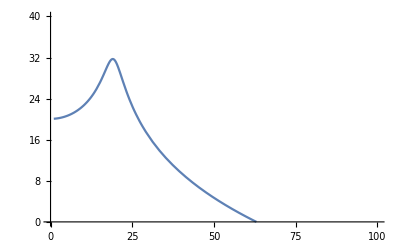

```mathematica
(* This looks like the simulation. *)
Plot[20 Log10[G0[215, 23.7, 10, 8.5*^5,3*^-7,1  10*^-12,2 π s 10^6]],{s,1,100},PlotRange->{0,40}]
```

```mathematica
Solve[Rf+Rg(1+ⅈ Lc s/Rt-Ct Lc s^2)==0,s](* zeros *)
Solve[(Rf/Rt+1)+ⅈ (Lc (Rf/Rs+1)/Rt+Ct Rf) s-Ct Lc (Rf/Rs+1) s^2==0,s](* poles *)
```

{{s→-(-√(4 Ct Lc Rg (Rf+Rg)-(Lc^2 Rg^2)/Rt^2)-(ⅈ Lc Rg)/Rt)/(2 Ct Lc Rg)},{s→-(√(4 Ct Lc Rg (Rf+Rg)-(Lc^2 Rg^2)/Rt^2)-(ⅈ Lc Rg)/Rt)/(2 Ct Lc Rg)}}

{{s→(ⅈ (Ct Rf-ⅈ √(-4 (-Ct Lc-(Ct Lc Rf)/Rs) (1+Rf/Rt)+(ⅈ Ct Rf+(ⅈ Lc)/Rt+(ⅈ Lc Rf)/(Rs Rt))^2)+Lc/Rt+(Lc Rf)/(Rs Rt)))/(2 (Ct Lc+(Ct Lc Rf)/Rs))},{s→(ⅈ (Ct Rf+ⅈ √(-4 (-Ct Lc-(Ct Lc Rf)/Rs) (1+Rf/Rt)+(ⅈ Ct Rf+(ⅈ Lc)/Rt+(ⅈ Lc Rf)/(Rs Rt))^2)+Lc/Rt+(Lc Rf)/(Rs Rt)))/(2 (Ct Lc+(Ct Lc Rf)/Rs))}}

```mathematica
(* Switch back to complex frequency *)
Solve[Rf+Rg(1+Lc s/Rt+Ct Lc s^2)==0,s](* zeros *)
Solve[(Rf/Rt+1)+(Lc (Rf/Rs+1)/Rt+Ct Rf) s+Ct Lc (Rf/Rs+1) s^2==0,s](* poles *)
```

{{s→(-√(-4 Ct Lc Rg (Rf+Rg)+(Lc^2 Rg^2)/Rt^2)-(Lc Rg)/Rt)/(2 Ct Lc Rg)},{s→(√(-4 Ct Lc Rg (Rf+Rg)+(Lc^2 Rg^2)/Rt^2)-(Lc Rg)/Rt)/(2 Ct Lc Rg)}}

{{s→(-Ct Rf-√(-4 (Ct Lc+(Ct Lc Rf)/Rs) (1+Rf/Rt)+(Ct Rf+Lc/Rt+(Lc Rf)/(Rs Rt))^2)-Lc/Rt-(Lc Rf)/(Rs Rt))/(2 (Ct Lc+(Ct Lc Rf)/Rs))},{s→(-Ct Rf+√(-4 (Ct Lc+(Ct Lc Rf)/Rs) (1+Rf/Rt)+(Ct Rf+Lc/Rt+(Lc Rf)/(Rs Rt))^2)-Lc/Rt-(Lc Rf)/(Rs Rt))/(2 (Ct Lc+(Ct Lc Rf)/Rs))}}

```mathematica
(* Without Lg, I get nonsense values for the zeros that I'm supposedly compensating. I think I need to proceed with finding the poles and zeros of the full transfer function *)
```

```mathematica
FullSimplify[ComplexExpand[(Rs (Rf Rt+Rg Rt+ⅈ Lc Rg s+ⅈ Lg Rt s-Lc Lg s^2-Ct Lc Rg Rt s^2-ⅈ Ct Lc Lg Rt s^3))/((Rg+ⅈ Lg s) (Rf Rs+Rs Rt+ⅈ Lc Rf s+ⅈ Lc Rs s+ⅈ Ct Rf Rs Rt s-Ct Lc Rf Rt s^2-Ct Lc Rs Rt s^2)) (Rs (Rf Rt+Rg Rt-ⅈ Lc Rg s-ⅈ Lg Rt s-Lc Lg s^2-Ct Lc Rg Rt s^2+ⅈ Ct Lc Lg Rt s^3))/((Rg-ⅈ Lg s) (Rf Rs+Rs Rt-ⅈ Lc Rf s-ⅈ Lc Rs s-ⅈ Ct Rf Rs Rt s-Ct Lc Rf Rt s^2-Ct Lc Rs Rt s^2))],Assumptions->{s∈Reals,Rt∈Reals,Ct∈Reals,Rg∈Reals,Rf∈Reals,Rs∈Reals,Lc∈Reals,Lg∈Reals}]
```

(Rs^2 (Rf^2 Rt^2+2 Rf Rt (Rg Rt-Lc (Lg+Ct Rg Rt) s^2)+(Rg^2+Lg^2 s^2) (Lc^2 s^2+Rt^2 (-1+Ct Lc s^2)^2)))/((Rg^2+Lg^2 s^2) (Rs^2 (Rf+Rt)^2+(Lc^2 (Rf+Rs)^2+Ct Rs (Ct Rf^2 Rs-2 Lc (Rf+Rs)) Rt^2) s^2+Ct^2 Lc^2 (Rf+Rs)^2 Rt^2 s^4))

```mathematica
G1[Rf_,Rg_,Rs_,Rt_,Lc_,Lg_,Ct_,s_]:=Sqrt[(Rs^2 (Rf^2 Rt^2+2 Rf Rt (Rg Rt-Lc (Lg+Ct Rg Rt) s^2)+(Rg^2+Lg^2 s^2) (Lc^2 s^2+Rt^2 (-1+Ct Lc s^2)^2)))/((Rg^2+Lg^2 s^2) (Rs^2 (Rf+Rt)^2+(Lc^2 (Rf+Rs)^2+Ct Rs (Ct Rf^2 Rs-2 Lc (Rf+Rs)) Rt^2) s^2+Ct^2 Lc^2 (Rf+Rs)^2 Rt^2 s^4))];
```

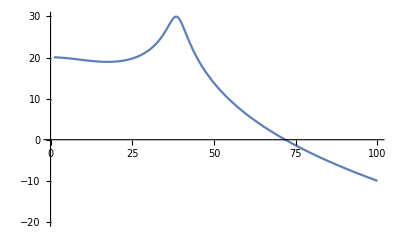

```mathematica
(* This looks like the simulation. *)
Plot[20 Log10[G1[215, 23.7, 10, 8.5*^5,3*^-7,2.2*^-7,.25  10*^-12,2 π s 10^6]],{s,1,100},PlotRange->{-20,30}]
```

```mathematica
Solve[Rs (Rf Rt+Rg Rt+Lc Rg s+Lg Rt s+Lc Lg s^2+Ct Lc Rg Rt s^2+Ct Lc Lg Rt s^3)==0,s]
Solve[(Rg+Lg s) (Rf Rs+Rs Rt+Lc Rf s+Lc Rs s+Ct Rf Rs Rt s+Ct Lc Rf Rt s^2+Ct Lc Rs Rt s^2) ==0,s]
```

{{s→-(Lc Lg+Ct Lc Rg Rt)/(3 Ct Lc Lg Rt)-(2^(1/3) (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2))/(3 Ct Lc Lg Rt (-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3+√((-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3)^2+4 (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2)^3))^(1/3))+1/(3 2^(1/3) Ct Lc Lg Rt)(-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3+√((-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3)^2+4 (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2)^3))^(1/3)},{s→-(Lc Lg+Ct Lc Rg Rt)/(3 Ct Lc Lg Rt)+((1+ⅈ √3) (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2))/(3 2^(2/3) Ct Lc Lg Rt (-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3+√((-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3)^2+4 (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2)^3))^(1/3))-1/(6 2^(1/3) Ct Lc Lg Rt)(1-ⅈ √3) (-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3+√((-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3)^2+4 (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2)^3))^(1/3)},{s→-(Lc Lg+Ct Lc Rg Rt)/(3 Ct Lc Lg Rt)+((1-ⅈ √3) (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2))/(3 2^(2/3) Ct Lc Lg Rt (-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3+√((-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3)^2+4 (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2)^3))^(1/3))-1/(6 2^(1/3) Ct Lc Lg Rt)(1+ⅈ √3) (-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3+√((-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3)^2+4 (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2)^3))^(1/3)}}

{{s→-Rg/Lg},{s→(-Lc Rf-Lc Rs-Ct Rf Rs Rt-√(-4 (Rf Rs+Rs Rt) (Ct Lc Rf Rt+Ct Lc Rs Rt)+(Lc Rf+Lc Rs+Ct Rf Rs Rt)^2))/(2 (Ct Lc Rf Rt+Ct Lc Rs Rt))},{s→(-Lc Rf-Lc Rs-Ct Rf Rs Rt+√(-4 (Rf Rs+Rs Rt) (Ct Lc Rf Rt+Ct Lc Rs Rt)+(Lc Rf+Lc Rs+Ct Rf Rs Rt)^2))/(2 (Ct Lc Rf Rt+Ct Lc Rs Rt))}}

```mathematica
FullSimplify[-(Lc Lg+Ct Lc Rg Rt)/(3 Ct Lc Lg Rt)-(2^(1/3) (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2))/(3 Ct Lc Lg Rt (-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3+√((-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3)^2+4 (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2)^3))^(1/3))+1/(3 2^(1/3) Ct Lc Lg Rt)(-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3+√((-2 Lc^3 Lg^3+3 Ct Lc^3 Lg^2 Rg Rt+9 Ct Lc^2 Lg^3 Rt^2+3 Ct^2 Lc^3 Lg Rg^2 Rt^2-27 Ct^2 Lc^2 Lg^2 Rf Rt^3-18 Ct^2 Lc^2 Lg^2 Rg Rt^3-2 Ct^3 Lc^3 Rg^3 Rt^3)^2+4 (3 Ct Lc Lg Rt (Lc Rg+Lg Rt)-(Lc Lg+Ct Lc Rg Rt)^2)^3))^(1/3)]
```

1/(6 Ct Lc Lg Rt)(-2 Lc (Lg+Ct Rg Rt)+(2 2^(1/3) Lc (Lc Lg^2-Ct Lc Lg Rg Rt+Ct (-3 Lg^2+Ct Lc Rg^2) Rt^2))/(-Lc^3 (Lg-2 Ct Rg Rt) (2 Lg-Ct Rg Rt) (Lg+Ct Rg Rt)+9 Ct Lc^2 Lg^2 Rt^2 (Lg-Ct (3 Rf+2 Rg) Rt)+√(Lc^3 (4 (3 Ct Lg Rt (Lc Rg+Lg Rt)-Lc (Lg+Ct Rg Rt)^2)^3+Lc (Lc (Lg-2 Ct Rg Rt) (2 Lg-Ct Rg Rt) (Lg+Ct Rg Rt)+9 Ct Lg^2 Rt^2 (-Lg+Ct (3 Rf+2 Rg) Rt))^2)))^(1/3)+2^(2/3) (-Lc^3 (Lg-2 Ct Rg Rt) (2 Lg-Ct Rg Rt) (Lg+Ct Rg Rt)+9 Ct Lc^2 Lg^2 Rt^2 (Lg-Ct (3 Rf+2 Rg) Rt)+√(Lc^3 (4 (3 Ct Lg Rt (Lc Rg+Lg Rt)-Lc (Lg+Ct Rg Rt)^2)^3+Lc (Lc (Lg-2 Ct Rg Rt) (2 Lg-Ct Rg Rt) (Lg+Ct Rg Rt)+9 Ct Lg^2 Rt^2 (-Lg+Ct (3 Rf+2 Rg) Rt))^2)))^(1/3))

#### Using Kirchoff, with Rm

```mathematica
(* Use Kirchoff's rules to get transfer function, including inverting input impedance *)
Eliminate[Vo-Vs==Io s Lc&& Vs==Is Rs&&Vs-Vm==Iff Rf&&Io==Iff+Is&&Vo/(Rt/(1+s Rt Ct))+Iff==Ig&&Vm==Ig (Rg+s Lg)&&Vin-Vm==Rm Vo/(Rt/(1+s Rt Ct)),{Io,Is,Ig,Iff,Vo, Vm}]
```

Rs (Rf+Rg+Lg s+(Lc Rg s)/Rt+Ct Lc Rg s^2+(Lc Lg s^2)/Rt+Ct Lc Lg s^3) Vin==(Rg Rs+(Rf Rg Rs)/Rt+(Rf Rm Rs)/Rt+(Rg Rm Rs)/Rt+Lg Rs s+Ct Rf Rg Rs s+Ct Rf Rm Rs s+Ct Rg Rm Rs s+(Lc Rf Rg s)/Rt+(Lc Rf Rm s)/Rt+(Lc Rg Rm s)/Rt+(Lg Rf Rs s)/Rt+(Lc Rg Rs s)/Rt+(Lc Rm Rs s)/Rt+(Lg Rm Rs s)/Rt+Ct Lc Rf Rg s^2+Ct Lc Rf Rm s^2+Ct Lc Rg Rm s^2+Ct Lg Rf Rs s^2+Ct Lc Rg Rs s^2+Ct Lc Rm Rs s^2+Ct Lg Rm Rs s^2+(Lc Lg Rf s^2)/Rt+(Lc Lg Rm s^2)/Rt+(Lc Lg Rs s^2)/Rt+Ct Lc Lg Rf s^3+Ct Lc Lg Rm s^3+Ct Lc Lg Rs s^3) Vs&&Rt≠0

```mathematica
Factor[Rs (Rf+Rg+Lg s+(Lc Rg s)/Rt+Ct Lc Rg s^2+(Lc Lg s^2)/Rt+Ct Lc Lg s^3)/(Rg Rs+(Rf Rg Rs)/Rt+(Rf Rm Rs)/Rt+(Rg Rm Rs)/Rt+Lg Rs s+Ct Rf Rg Rs s+Ct Rf Rm Rs s+Ct Rg Rm Rs s+(Lc Rf Rg s)/Rt+(Lc Rf Rm s)/Rt+(Lc Rg Rm s)/Rt+(Lg Rf Rs s)/Rt+(Lc Rg Rs s)/Rt+(Lc Rm Rs s)/Rt+(Lg Rm Rs s)/Rt+Ct Lc Rf Rg s^2+Ct Lc Rf Rm s^2+Ct Lc Rg Rm s^2+Ct Lg Rf Rs s^2+Ct Lc Rg Rs s^2+Ct Lc Rm Rs s^2+Ct Lg Rm Rs s^2+(Lc Lg Rf s^2)/Rt+(Lc Lg Rm s^2)/Rt+(Lc Lg Rs s^2)/Rt+Ct Lc Lg Rf s^3+Ct Lc Lg Rm s^3+Ct Lc Lg Rs s^3)]
```

(Rs (Rf Rt+Rg Rt+Lc Rg s+Lg Rt s+Lc Lg s^2+Ct Lc Rg Rt s^2+Ct Lc Lg Rt s^3))/(Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+Lc Rf Rg s+Lc Rf Rm s+Lc Rg Rm s+Lg Rf Rs s+Lc Rg Rs s+Lc Rm Rs s+Lg Rm Rs s+Lg Rs Rt s+Ct Rf Rg Rs Rt s+Ct Rf Rm Rs Rt s+Ct Rg Rm Rs Rt s+Lc Lg Rf s^2+Lc Lg Rm s^2+Lc Lg Rs s^2+Ct Lc Rf Rg Rt s^2+Ct Lc Rf Rm Rt s^2+Ct Lc Rg Rm Rt s^2+Ct Lg Rf Rs Rt s^2+Ct Lc Rg Rs Rt s^2+Ct Lc Rm Rs Rt s^2+Ct Lg Rm Rs Rt s^2+Ct Lc Lg Rf Rt s^3+Ct Lc Lg Rm Rt s^3+Ct Lc Lg Rs Rt s^3)

```mathematica
(* Transfer function without Lg *)
FullSimplify[(Rs (Rf Rt+Rg Rt+Lc Rg s+Lg Rt s+Lc Lg s^2+Ct Lc Rg Rt s^2+Ct Lc Lg Rt s^3))/(Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+Lc Rf Rg s+Lc Rf Rm s+Lc Rg Rm s+Lg Rf Rs s+Lc Rg Rs s+Lc Rm Rs s+Lg Rm Rs s+Lg Rs Rt s+Ct Rf Rg Rs Rt s+Ct Rf Rm Rs Rt s+Ct Rg Rm Rs Rt s+Lc Lg Rf s^2+Lc Lg Rm s^2+Lc Lg Rs s^2+Ct Lc Rf Rg Rt s^2+Ct Lc Rf Rm Rt s^2+Ct Lc Rg Rm Rt s^2+Ct Lg Rf Rs Rt s^2+Ct Lc Rg Rs Rt s^2+Ct Lc Rm Rs Rt s^2+Ct Lg Rm Rs Rt s^2+Ct Lc Lg Rf Rt s^3+Ct Lc Lg Rm Rt s^3+Ct Lc Lg Rs Rt s^3)/.Lg->0]
```

(Rs (Rf Rt+Rg (Rt+Lc s+Ct Lc Rt s^2)))/(Lc Rm Rs s (1+Ct Rt s)+Rg Rm (Rs+Lc s) (1+Ct Rt s)+Rf (Rg+Rm) (Rs+Lc s) (1+Ct Rt s)+Rg Rs (Rt+Lc s+Ct Lc Rt s^2))

```mathematica
Collect[(Lc Rm Rs s (1+Ct Rt s)+Rg Rm (Rs+Lc s) (1+Ct Rt s)+Rf (Rg+Rm) (Rs+Lc s) (1+Ct Rt s)+Rg Rs (Rt+Lc s+Ct Lc Rt s^2)),s]
```

Rg Rm Rs+Rf (Rg+Rm) Rs+Rg Rs Rt+(Lc Rg Rm+Lc Rf (Rg+Rm)+Lc Rg Rs+Lc Rm Rs+Ct Rg Rm Rs Rt+Ct Rf (Rg+Rm) Rs Rt) s+(Ct Lc Rg Rm Rt+Ct Lc Rf (Rg+Rm) Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt) s^2

```mathematica
Simplify[(Rg Rm Rs+Rf (Rg+Rm) Rs+Rg Rs Rt)/(Ct Lc Rg Rm Rt+Ct Lc Rf (Rg+Rm) Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt)]
```

(Rs (Rf (Rg+Rm)+Rg (Rm+Rt)))/(Ct Lc (Rf (Rg+Rm)+Rm Rs+Rg (Rm+Rs)) Rt)

```mathematica
FullSimplify[(Rs (Rf (Rg+Rm)+Rg (Rm+Rt)))/((Rf (Rg+Rm)+Rm Rs+Rg (Rm+Rs)) Rt)]
```

(Rs (Rf (Rg+Rm)+Rg (Rm+Rt)))/((Rf (Rg+Rm)+Rm Rs+Rg (Rm+Rs)) Rt)

```mathematica
(* Verify DC gain *)
FullSimplify[((Rs (Rf Rt+Rg (Rt+Lc s+Ct Lc Rt s^2)))/(Lc Rm Rs s (1+Ct Rt s)+Rg Rm (Rs+Lc s) (1+Ct Rt s)+Rf (Rg+Rm) (Rs+Lc s) (1+Ct Rt s)+Rg Rs (Rt+Lc s+Ct Lc Rt s^2)))/.s->0]
```

((Rf+Rg) Rt)/(Rf (Rg+Rm)+Rg (Rm+Rt))

```mathematica
(* Transfer function with Lg *)
FullSimplify[(Rs (Rf Rt+Rg Rt+Lc Rg s+Lg Rt s+Lc Lg s^2+Ct Lc Rg Rt s^2+Ct Lc Lg Rt s^3))/(Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+Lc Rf Rg s+Lc Rf Rm s+Lc Rg Rm s+Lg Rf Rs s+Lc Rg Rs s+Lc Rm Rs s+Lg Rm Rs s+Lg Rs Rt s+Ct Rf Rg Rs Rt s+Ct Rf Rm Rs Rt s+Ct Rg Rm Rs Rt s+Lc Lg Rf s^2+Lc Lg Rm s^2+Lc Lg Rs s^2+Ct Lc Rf Rg Rt s^2+Ct Lc Rf Rm Rt s^2+Ct Lc Rg Rm Rt s^2+Ct Lg Rf Rs Rt s^2+Ct Lc Rg Rs Rt s^2+Ct Lc Rm Rs Rt s^2+Ct Lg Rm Rs Rt s^2+Ct Lc Lg Rf Rt s^3+Ct Lc Lg Rm Rt s^3+Ct Lc Lg Rs Rt s^3)]
```

(Rs (Rf Rt+(Rg+Lg s) (Rt+Lc s+Ct Lc Rt s^2)))/(Rg Rm (Rs+Lc s) (1+Ct Rt s)+Rf (Rs+Lc s) (Rg+Rm+Lg s) (1+Ct Rt s)+Lc s (Rm Rs+Lg (Rm+Rs) s) (1+Ct Rt s)+Lg Rs s (Rm+Rt+Ct Rm Rt s)+Rg Rs (Rt+Lc s+Ct Lc Rt s^2))

```mathematica
Factor[(Rg Rm (Rs+Lc s) (1+Ct Rt s)+Rf (Rs+Lc s) (Rg+Rm+Lg s) (1+Ct Rt s)+Lc s (Rm Rs+Lg (Rm+Rs) s) (1+Ct Rt s)+Lg Rs s (Rm+Rt+Ct Rm Rt s)+Rg Rs (Rt+Lc s+Ct Lc Rt s^2))]
```

Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+Lc Rf Rg s+Lc Rf Rm s+Lc Rg Rm s+Lg Rf Rs s+Lc Rg Rs s+Lc Rm Rs s+Lg Rm Rs s+Lg Rs Rt s+Ct Rf Rg Rs Rt s+Ct Rf Rm Rs Rt s+Ct Rg Rm Rs Rt s+Lc Lg Rf s^2+Lc Lg Rm s^2+Lc Lg Rs s^2+Ct Lc Rf Rg Rt s^2+Ct Lc Rf Rm Rt s^2+Ct Lc Rg Rm Rt s^2+Ct Lg Rf Rs Rt s^2+Ct Lc Rg Rs Rt s^2+Ct Lc Rm Rs Rt s^2+Ct Lg Rm Rs Rt s^2+Ct Lc Lg Rf Rt s^3+Ct Lc Lg Rm Rt s^3+Ct Lc Lg Rs Rt s^3

```mathematica
Collect[Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+Lc Rf Rg s+Lc Rf Rm s+Lc Rg Rm s+Lg Rf Rs s+Lc Rg Rs s+Lc Rm Rs s+Lg Rm Rs s+Lg Rs Rt s+Ct Rf Rg Rs Rt s+Ct Rf Rm Rs Rt s+Ct Rg Rm Rs Rt s+Lc Lg Rf s^2+Lc Lg Rm s^2+Lc Lg Rs s^2+Ct Lc Rf Rg Rt s^2+Ct Lc Rf Rm Rt s^2+Ct Lc Rg Rm Rt s^2+Ct Lg Rf Rs Rt s^2+Ct Lc Rg Rs Rt s^2+Ct Lc Rm Rs Rt s^2+Ct Lg Rm Rs Rt s^2+Ct Lc Lg Rf Rt s^3+Ct Lc Lg Rm Rt s^3+Ct Lc Lg Rs Rt s^3,s]
```

Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+(Lc Rf Rg+Lc Rf Rm+Lc Rg Rm+Lg Rf Rs+Lc Rg Rs+Lc Rm Rs+Lg Rm Rs+Lg Rs Rt+Ct Rf Rg Rs Rt+Ct Rf Rm Rs Rt+Ct Rg Rm Rs Rt) s+(Lc Lg Rf+Lc Lg Rm+Lc Lg Rs+Ct Lc Rf Rg Rt+Ct Lc Rf Rm Rt+Ct Lc Rg Rm Rt+Ct Lg Rf Rs Rt+Ct Lc Rg Rs Rt+Ct Lc Rm Rs Rt+Ct Lg Rm Rs Rt) s^2+(Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt) s^3

```mathematica
Collect[(Rs (Rf Rt+(Rg+Lg s) (Rt+Lc s+Ct Lc Rt s^2))),s]
```

Rs (Rf Rt+Rg Rt)+Rs (Lc Rg+Lg Rt) s+Rs (Lc Lg+Ct Lc Rg Rt) s^2+Ct Lc Lg Rs Rt s^3

```mathematica
(Rs (Rf Rt+Rg Rt+Lc Rg s+Lg Rt s+Lc Lg s^2+Ct Lc Rg Rt s^2+Ct Lc Lg Rt s^3))/(Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+Lc Rf Rg s+Lc Rf Rm s+Lc Rg Rm s+Lg Rf Rs s+Lc Rg Rs s+Lc Rm Rs s+Lg Rm Rs s+Lg Rs Rt s+Ct Rf Rg Rs Rt s+Ct Rf Rm Rs Rt s+Ct Rg Rm Rs Rt s+Lc Lg Rf s^2+Lc Lg Rm s^2+Lc Lg Rs s^2+Ct Lc Rf Rg Rt s^2+Ct Lc Rf Rm Rt s^2+Ct Lc Rg Rm Rt s^2+Ct Lg Rf Rs Rt s^2+Ct Lc Rg Rs Rt s^2+Ct Lc Rm Rs Rt s^2+Ct Lg Rm Rs Rt s^2+Ct Lc Lg Rf Rt s^3+Ct Lc Lg Rm Rt s^3+Ct Lc Lg Rs Rt s^3)/.s->ⅈ s
```

(Rs (Rf Rt+Rg Rt+ⅈ Lc Rg s+ⅈ Lg Rt s-Lc Lg s^2-Ct Lc Rg Rt s^2-ⅈ Ct Lc Lg Rt s^3))/(Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+ⅈ Lc Rf Rg s+ⅈ Lc Rf Rm s+ⅈ Lc Rg Rm s+ⅈ Lg Rf Rs s+ⅈ Lc Rg Rs s+ⅈ Lc Rm Rs s+ⅈ Lg Rm Rs s+ⅈ Lg Rs Rt s+ⅈ Ct Rf Rg Rs Rt s+ⅈ Ct Rf Rm Rs Rt s+ⅈ Ct Rg Rm Rs Rt s-Lc Lg Rf s^2-Lc Lg Rm s^2-Lc Lg Rs s^2-Ct Lc Rf Rg Rt s^2-Ct Lc Rf Rm Rt s^2-Ct Lc Rg Rm Rt s^2-Ct Lg Rf Rs Rt s^2-Ct Lc Rg Rs Rt s^2-Ct Lc Rm Rs Rt s^2-Ct Lg Rm Rs Rt s^2-ⅈ Ct Lc Lg Rf Rt s^3-ⅈ Ct Lc Lg Rm Rt s^3-ⅈ Ct Lc Lg Rs Rt s^3)

```mathematica
ComplexExpand[(Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+ⅈ Lc Rf Rg s+ⅈ Lc Rf Rm s+ⅈ Lc Rg Rm s+ⅈ Lg Rf Rs s+ⅈ Lc Rg Rs s+ⅈ Lc Rm Rs s+ⅈ Lg Rm Rs s+ⅈ Lg Rs Rt s+ⅈ Ct Rf Rg Rs Rt s+ⅈ Ct Rf Rm Rs Rt s+ⅈ Ct Rg Rm Rs Rt s-Lc Lg Rf s^2-Lc Lg Rm s^2-Lc Lg Rs s^2-Ct Lc Rf Rg Rt s^2-Ct Lc Rf Rm Rt s^2-Ct Lc Rg Rm Rt s^2-Ct Lg Rf Rs Rt s^2-Ct Lc Rg Rs Rt s^2-Ct Lc Rm Rs Rt s^2-Ct Lg Rm Rs Rt s^2-ⅈ Ct Lc Lg Rf Rt s^3-ⅈ Ct Lc Lg Rm Rt s^3-ⅈ Ct Lc Lg Rs Rt s^3)]
```

Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt-Lc Lg Rf s^2-Lc Lg Rm s^2-Lc Lg Rs s^2-Ct Lc Rf Rg Rt s^2-Ct Lc Rf Rm Rt s^2-Ct Lc Rg Rm Rt s^2-Ct Lg Rf Rs Rt s^2-Ct Lc Rg Rs Rt s^2-Ct Lc Rm Rs Rt s^2-Ct Lg Rm Rs Rt s^2+ⅈ (Lc Rf Rg s+Lc Rf Rm s+Lc Rg Rm s+Lg Rf Rs s+Lc Rg Rs s+Lc Rm Rs s+Lg Rm Rs s+Lg Rs Rt s+Ct Rf Rg Rs Rt s+Ct Rf Rm Rs Rt s+Ct Rg Rm Rs Rt s-Ct Lc Lg Rf Rt s^3-Ct Lc Lg Rm Rt s^3-Ct Lc Lg Rs Rt s^3)

```mathematica
Solve[Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt-Lc Lg Rf s^2-Lc Lg Rm s^2-Lc Lg Rs s^2-Ct Lc Rf Rg Rt s^2-Ct Lc Rf Rm Rt s^2-Ct Lc Rg Rm Rt s^2-Ct Lg Rf Rs Rt s^2-Ct Lc Rg Rs Rt s^2-Ct Lc Rm Rs Rt s^2-Ct Lg Rm Rs Rt s^2+ⅈ (Lc Rf Rg s+Lc Rf Rm s+Lc Rg Rm s+Lg Rf Rs s+Lc Rg Rs s+Lc Rm Rs s+Lg Rm Rs s+Lg Rs Rt s+Ct Rf Rg Rs Rt s+Ct Rf Rm Rs Rt s+Ct Rg Rm Rs Rt s-Ct Lc Lg Rf Rt s^3-Ct Lc Lg Rm Rt s^3-Ct Lc Lg Rs Rt s^3)==0,s]
```

{{s→-(ⅈ (-Lc Lg Rf-Lc Lg Rm-Lc Lg Rs-Ct Lc Rf Rg Rt-Ct Lc Rf Rm Rt-Ct 3 Rt-Ct Lg Rf Rs Rt-Ct Lc Rg Rs Rt-Ct Lc Rm Rs Rt-Ct Lg Rm Rs Rt))/(3 (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt))-(ⅈ 2^1 (1))/(3 (1) 1)+(ⅈ (1)^(1/3))/(3 2^1 (Ct Lc Lg Rf Rt+Ct Lc Lg Rm Rt+Ct Lc Lg Rs Rt))},{s→1},{s→1}}
 |  |  |  |

```mathematica
FullSimplify[ComplexExpand[(Rs (Rf Rt+Rg Rt+ⅈ Lc Rg s+ⅈ Lg Rt s-Lc Lg s^2-Ct Lc Rg Rt s^2-ⅈ Ct Lc Lg Rt s^3))/(Rf Rg Rs+Rf Rm Rs+Rg Rm Rs+Rg Rs Rt+ⅈ Lc Rf Rg s+ⅈ Lc Rf Rm s+ⅈ Lc Rg Rm s+ⅈ Lg Rf Rs s+ⅈ Lc Rg Rs s+ⅈ Lc Rm Rs s+ⅈ Lg Rm Rs s+ⅈ Lg Rs Rt s+ⅈ Ct Rf Rg Rs Rt s+ⅈ Ct Rf Rm Rs Rt s+ⅈ Ct Rg Rm Rs Rt s-Lc Lg Rf s^2-Lc Lg Rm s^2-Lc Lg Rs s^2-Ct Lc Rf Rg Rt s^2-Ct Lc Rf Rm Rt s^2-Ct Lc Rg Rm Rt s^2-Ct Lg Rf Rs Rt s^2-Ct Lc Rg Rs Rt s^2-Ct Lc Rm Rs Rt s^2-Ct Lg Rm Rs Rt s^2-ⅈ Ct Lc Lg Rf Rt s^3-ⅈ Ct Lc Lg Rm Rt s^3-ⅈ Ct Lc Lg Rs Rt s^3)],Assumptions->{s∈Reals,Rt∈Reals,Ct∈Reals,Rg∈Reals,Rf∈Reals,Rs∈Reals,Lc∈Reals,Lg∈Reals,Ri∈Reals}]
```

$Aborted

### To Litz or not to Litz

```mathematica
μ0=4 π 10^-7;
μc=μ0 1.26 10^-6;
delta[f_]:=Sqrt[2 1.68 10^-8/(2 π f μc)];
delta2[f_]:=503 Sqrt[1.68 10^-8/f] 10^6;
```

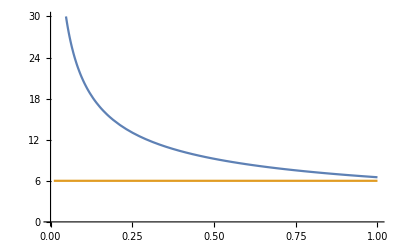

```mathematica
Plot[{delta2[f],6},{f,10^6,10^8},PlotRange->{0,30}]
```

```mathematica
Ap[w_,f_]:=If[2 delta2[f]<35,2 delta2[f] (35-2 delta2[f])+2 delta2[f] w,1];
Al[w_,f_,Nc_]:=If[2 delta2[f]<35,2 delta2[f] (35-2 delta2[f]) Nc+2 delta2[f] w,1];
```

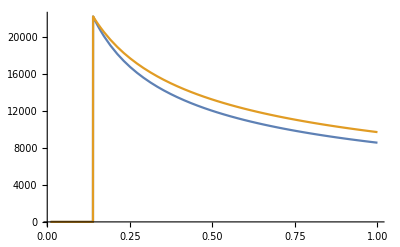

```mathematica
Plot[{Ap[5*127,f],Al[5*127,f,5]},{f,10^6,10^8}]
```

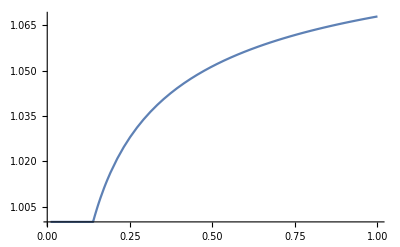

```mathematica
Plot[{Al[5*254,f,5]/Ap[5*254,f]},{f,10^6,10^8}]
```

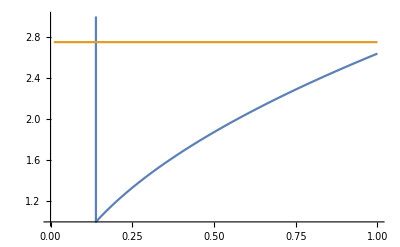

```mathematica
Plot[{35*5*254/Ap[5*254,f],2.75},{f,10^6,10^8},PlotRange->{1,3}]
```

```mathematica
Solve[77.3==Sqrt[(150*10^-9/200)/cc],cc]
200*cc /.%
```

{{cc→1.25517×10^-13}}

{2.51034×10^-11}

```mathematica
.015*1.4
```

0.021

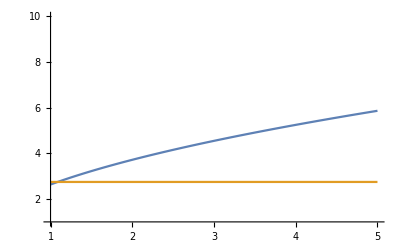

```mathematica
Plot[{35*50*25.4/Ap[50*25.4,f],2.75},{f,10^8,5 10^8},PlotRange->{1,10}]
```

## Microwave Antenna Design

```mathematica
c=3*^8;(*m/s*)
H=1.5*^-3;(*FR4 thickness, m*)
Er=3.9;(*FR4 dielectric constant*)
eta=376.7;(*impedance of free space, ohms*)
Er2=2.55;
H2=1.6*^-3;
```

### λ/2 patch first pass

```mathematica
w[f_,er_]:=c/(2 f Sqrt[er]);(*First width estimate, m*)
eff[f_,er_,h_]:=(er+1)/2+(er-1)/2 (1+(10h)/w[f,er])^(-1/2);(*effective dielectric constant*)
Δ[f_,er_,h_]:=0.412 h (eff[f,er,h]+0.300)/(eff[f,er,h]-0.258)(w[f,er]/h+0.262)/(w[f,er]/h+0.813);(*length correction, m*)
L[f_,er_,h_]:=c/(2 f Sqrt[eff[f,er,h]])-2 Δ[f,er,h];(*resonant length, m*)
G[f_,er_,h_]:=(π L[f,er,h])/(eta c/f) (1-(2 π f h/c)^2/24);(*Conductance of side slot, siemens*)
R[f_,er_,h_]:=1/(2 G[f,er,h]);(*Input impedance of patch, ohms*)
x[f_,er_,h_]:=L[f,er,h]/π ArcSin[(50/R[f,er,h])^(1/4)];(*50 ohm feedpoint, m from center*)
```

```mathematica
(* Check against example in text *)
w[3*^9,Er2]*1000
eff[3*^9,Er2,H2]
L[3*^9,Er2,H2]*1000
x[3*^9,Er2,H2]*1000
```

31.3112

2.40548

30.622

7.70664

```mathematica
(* 6.8 GHz for 87Rb *)
w[6.6*^9,Er]*1000
eff[6.6*^9,Er,H]
L[6.6*^9,Er,H]*1000
x[6.6*^9,Er,H]*1000
```

11.5084

3.4054

10.9552

2.55689

```mathematica
(* 3.0 GHz for 85Rb*)
w[2.9*^9,Er]*1000
eff[2.9*^9,Er,H]
L[2.9*^9,Er,H]*1000
x[2.9*^9,Er,H]*1000
```

26.1915

3.60623

25.8389

6.10009

### λ\2 patch 2nd pass

```mathematica
(*Use recursion to get better info*)
eff2[f_,er_,h_]:=(er+1)/2+(er-1)/2 (1+(10h)/L[f,er,h])^(-1/2);
Δ2[f_,er_,h_]:=0.412 h (eff2[f,er,h]+0.300)/(eff2[f,er,h]-0.258)(L[f,er,h]/h+0.262)/(L[f,er,h]/h+0.813);
L2[f_,er_,h_]:=c/(2 f Sqrt[eff2[f,er,h]])-2 Δ2[f,er,h];
G2[f_,er_,h_]:=(π L2[f,er,h])/(eta c/f) (1-(2 π f h/c)^2/24);(*Conductance of side slot, siemens*)
R2[f_,er_,h_]:=1/(2 G2[f,er,h]);(*Input impedance of patch, ohms*)
x2[f_,er_,h_]:=L2[f,er,h]/π ArcSin[(50/R2[f,er,h])^(1/4)];
```

```mathematica
(* Check example in text *)
eff2[3*^9,Er2,H2]
L2[3*^9,Er2,H2]*1000
```

2.40309

30.6386

```mathematica
(* 6.8 GHz for Rb *)
eff2[6.6*^9,Er,H]
L2[6.6*^9,Er,H]*1000
x2[6.6*^9,Er,H]*1000
```

3.39203

10.9828

2.56533

```mathematica
(* 3.0 GHz for 85Rb*)
eff2[2.9*^9,Er,H]
L2[2.9*^9,Er,H]*1000
x2[2.9*^9,Er,H]*1000
```

3.60337

25.8502

6.10356

### λ/4 patch

```mathematica
R4[f_,er_,h_]:=1/(G2[f,er,h]);(*Input impedance of patch, ohms*)
x4[f_,er_,h_]:=L2[f,er,h]/π ArcSin[(50/R4[f,er,h])^(1/4)];
```

```mathematica
(* 6.8 GHz for Rb *)
R4[6.8*^9,Er,H]
x4[6.8*^9,Er,H]*1000
```

498.238

2.02425

```mathematica
(* 3.0 GHz for Rb *)
R4[2.9*^9,Er,H]
x4[2.9*^9,Er,H]*1000
```

480.016

4.97159

### Curved Dipole

```mathematica
Ld[f_,er_]:=c/(4 f Sqrt[er]);(* Length of dipole leg, m*)
λeff[f_,er_]:=c/(f Sqrt[er]);(* Effective wavelength, m*)
```

```mathematica
Ld[800*^6,1]//N
```

0.09375

#### Lithium-7

```mathematica
Ld[800*^6,Er]
```

0.0474722

```mathematica
λeff[800*^6,Er]
```

0.189889

```mathematica
2 π 1.22 2.54
```

19.4703

#### Lithium-6

```mathematica
Ld[230*^6,Er]
Ld[230*^6,4.5]
```

0.165121

0.153719

```mathematica
R
```

```mathematica
λeff[230*^6,Er]
```

0.660482

```mathematica
2 π 1.22 2.54
```

19.4703

### Ring Impedance Matching

```mathematica
Solve[(1+(R1+ⅈ s L) ⅈ s C1)/(R1+ⅈ s L1)==0,{s}]
```

{{s→-(-ⅈ C1 R1-√(4 C1 L-C1^2 R1^2))/(2 C1 L)},{s→-(-ⅈ C1 R1+√(4 C1 L-C1^2 R1^2))/(2 C1 L)}}

```mathematica
Simplify[(-(-ⅈ C1 R1-√(4 C1 L-C1^2 R1^2))/(2 C1 L)) (-(ⅈ C1 R1-√(4 C1 L-C1^2 R1^2))/(2 C1 L))]
Simplify[(-(-ⅈ C1 R1+√(4 C1 L-C1^2 R1^2))/(2 C1 L)) (-(ⅈ C1 R1+√(4 C1 L-C1^2 R1^2))/(2 C1 L))]
```

1/(C1 L)

1/(C1 L)

```mathematica
Solve[(R1+ⅈ s L1+1/(ⅈ s C1))/((R1+ⅈ s L1)/(ⅈ s C1))==0,{s}]
```

{{s→-(ⅈ (-C1 R1+√C1 √(-4 L1+C1 R1^2)))/(2 C1 L1)},{s→(ⅈ (C1 R1+√C1 √(-4 L1+C1 R1^2)))/(2 C1 L1)}}

```mathematica
Solve[((R1+ⅈ s L1)/(ⅈ s C1))/(R1+ⅈ s L1+1/(ⅈ s C1))==0,{s}]
```

{{s→(ⅈ R1)/L1}}

```mathematica
Simplify[(R1+ⅈ s L1+1/(ⅈ s C1))/((R1+ⅈ s L1)/(ⅈ s C1)) (R1-ⅈ s L1-1/(ⅈ s C1))/((R1-ⅈ s L1)/(-ⅈ s C1))]
```

(1-2 C1 L1 s^2+C1^2 s^2 (R1^2+L1^2 s^2))/(R1^2+L1^2 s^2)

```mathematica
Simplify[Sqrt[(1-2 C1 L1 s^2+C1^2 s^2 (R1^2+L1^2 s^2))/(R1^2+L1^2 s^2)]]
```

√((1-2 C1 L1 s^2+C1^2 s^2 (R1^2+L1^2 s^2))/(R1^2+L1^2 s^2))

```mathematica
Solve[√((1-2 C1 L1 s^2+C1^2 s^2 (R1^2+L1^2 s^2))/(R1^2+L1^2 s^2))==0,{s}]
```

{{s→-(√(2/(C1 L1)-R1^2/L1^2-(R1 √(-4 L1+C1 R1^2))/(√C1 L1^2)))/(√2)},{s→(√(2/(C1 L1)-R1^2/L1^2-(R1 √(-4 L1+C1 R1^2))/(√C1 L1^2)))/(√2)},{s→-√(1/(C1 L1)-R1^2/(2 L1^2)+(R1 √(-4 L1+C1 R1^2))/(2 √C1 L1^2))},{s→√(1/(C1 L1)-R1^2/(2 L1^2)+(R1 √(-4 L1+C1 R1^2))/(2 √C1 L1^2))}}

```mathematica
FullSimplify[(√(2/(C1 L1)-R1^2/L1^2-(R1 √(-4 L1+C1 R1^2))/(√C1 L1^2)))/(√2)]
```

√2 √(1/(2 C1 L1-C1^2 R1^2+C1^(3/2) R1 √(-4 L1+C1 R1^2)))

```mathematica
C1[ω_,L_,R_]:=Sqrt[R/50]/(ω^2 L)
C2[ω_,L_,R_]:=(1-Sqrt[R/50])/(ω^2 L)
```

```mathematica
C1[2 π 130*^6,160*^-9,0.1]
C2[2 π 130*^6,160*^-9,0.1]
```

4.18937×10^-13

8.94878×10^-12

### Rabi Frequency

```mathematica
μb=1.4*^3;(*Bohr Magneton, kHz/G*)
gf=1/2;(*For alkali boson gs*)
Ω[B_]:=gf μb B;(* kHz *)
```

```mathematica
Ω[32*^-3]
```

22.4

## Loop antenna impedance

```mathematica
μ0=4 π 10^-7; (*H/m*)
r0=1.22*.0254;(*loop radius in m*)
w=0.05*.0254;(*loop width in m*)
h=35*^-6;(*loop height in m*)
ρ=1.68 10^-8;(*copper resistivity, Ohm*m*)
```

```mathematica
w//N
```

0.00127

```mathematica
Solve[w*h==π r^2,r]
```

{{r→-0.000118949},{r→0.000118949}}

```mathematica
wr=1.2*^-4;(*effective wire radius of loop*)
```

```mathematica
La[a_,b_]:=μ0 a (Log[8 a/b]-2)(*external reactance, loop radius a, wire radius b*)
Li[a_,b_,f_]:=(a/(2 π f b)) Sqrt[2 π f μ0 ρ/2]
```

```mathematica
La[r0,wr]
Li[r0,wr,1 10^6]
```

2.291×10^-7

1.05844×10^-8

```mathematica
hs=delta2[100*^6]/10^6
Solve[2 w hs==π r^2,r]
```

6.51963×10^-6

{{r→-0.0000726028},{r→0.0000726028}}

```mathematica
ws=72*^-6;
```

```mathematica
La[r0,ws]
Li[r0,ws,1 10^6]
```

2.39257×10^-7

1.76407×10^-8

```mathematica
2 w+2 h
2 π wr
```

0.00261

0.000753982

```mathematica
La[r0,h]
Li[r0,h,1 10^6]
```

2.67345×10^-7

3.62894×10^-8

```mathematica
2 π r0 ρ/(w h)
```

0.0735887

```mathematica
2 π r0 ρ/(π h^2)
```

0.849957

```mathematica
R[a_,b_,f_]:=2 π a ρ/(π (delta2[f]/1*^6) (2 b-delta2[f]/1*^6))
```

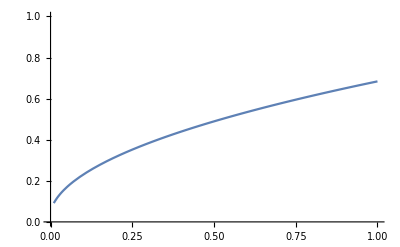

```mathematica
Plot[R[r0,wr,f],{f,1*^6, 100*^6},PlotRange->{0,1}]
```